```mathematica
Manipulate[Plot[Cos[k x]^2 -A Cos[k/2 x+π ϕ]^2/.{k->2π},{x,-2,2}],{ϕ,0,1},{{A,1},-1,2}]
```

### https://arxiv.org/pdf/1507.05937.pdf

```mathematica
RotationMatrix[-θ/2].({{Exp[I π/2], 0}, {0, 1}}).RotationMatrix[-π/4].({{1, 0}, {0, Exp[I θ]}}).RotationMatrix[π/4].{1,0}//FullSimplify
```

{ⅈ ⅇ^((ⅈ θ)/2),0}

```mathematica
({{Exp[I π/2], 0}, {0, 1}}).RotationMatrix[-π/4].({{1, 0}, {0, Exp[I θ]}}).RotationMatrix[π/4].{1,0}//FullSimplify
```

{1/2 ⅈ (1+ⅇ^(ⅈ θ)),1/2 (-1+ⅇ^(ⅈ θ))}

```mathematica
-RotationMatrix[θ/2].({{Exp[I π/2], 0}, {0, 1}}).({{1, 0}, {0, 1}}).({{Exp[I π/2], 0}, {0, 1}}).RotationMatrix[θ/2].{1,0}//FullSimplify
```

{1,0}

```mathematica
Esuper = FullSimplify[ExpToTrig[Exp[I k x]*{Cos[θ/2],Sin[θ/2]} + Exp[-I k x+I ϕ]*{Cos[θ/2],-Sin[θ/2]}]]
```

{2 ⅇ^((ⅈ ϕ)/2) Cos[θ/2] Cos[k x-ϕ/2],2 ⅈ ⅇ^((ⅈ ϕ)/2) Sin[θ/2] Sin[k x-ϕ/2]}

```mathematica
ComplexExpand[Total[Abs[FullSimplify[ExpToTrig[Exp[I k x]*{Cos[θ/2],Sin[θ/2]} + Exp[-I k x+I ϕ]*{Cos[θ/2],-Sin[θ/2]}]]]^2]/.{ϕ->ϕ}]//FullSimplify
```

2+2 Cos[θ] Cos[2 k x-ϕ]

```mathematica
ComplexExpand[Cross[Conjugate[
{2 ⅇ^((ⅈ ϕ)/2) Cos[θ/2] Cos[k x-ϕ/2],2 ⅈ ⅇ^((ⅈ ϕ)/2) Sin[θ/2] Sin[k x-ϕ/2],0}],
{2 ⅇ^((ⅈ ϕ)/2) Cos[θ/2] Cos[k x-ϕ/2],2 ⅈ ⅇ^((ⅈ ϕ)/2) Sin[θ/2] Sin[k x-ϕ/2],0}]]//FullSimplify
```

{0,0,2 ⅈ Sin[θ] Sin[2 k x-ϕ]}

```mathematica
{1,-I}.Esuper//FullSimplify
{1,I}.Esuper//FullSimplify
```

2 ⅇ^((ⅈ ϕ)/2) Cos[k x-θ/2-ϕ/2]

2 ⅇ^((ⅈ ϕ)/2) Cos[1/2 (2 k x+θ-ϕ)]

```mathematica
Cos[k x + θ/2]^2+Cos[k x - θ/2]^2//FullSimplify
```

1+Cos[2 k x] Cos[θ]

```mathematica
Manipulate[Plot[{Cos[k x]^2 +A Cos[k/2 x+π ϕ]^2+ B Sin[θ] Sin[2 k x+ψ π]/.{k->2π,θ->π/2},
Cos[k x]^2 +A Cos[k/2 x+π ϕ]^2- 2*B Sin[θ] Sin[2 k x+ψ π]/.{k->2π,θ->π/2}},{x,-2,2}],{ϕ,0,1},{{A,1},-1,2},{{B,0.1},0,1},{ψ,0,1}]
```

```mathematica
Manipulate[Plot[{Cos[k x]^2 +A Cos[k/2 x+π ϕ]^2+ B Sin[θ] Sin[2 k x+ψ π]/.{k->2π,θ->π/2},
Cos[k x]^2 +A Cos[k/2 x+π ϕ]^2- 2*B Sin[θ] Sin[2 k x+ψ π]/.{k->2π,θ->π/2}},{x,-1,1}],{ϕ,0,1},{{A,1},-1,2},{{B,0.1},0,1},{ψ,0,1}]
```

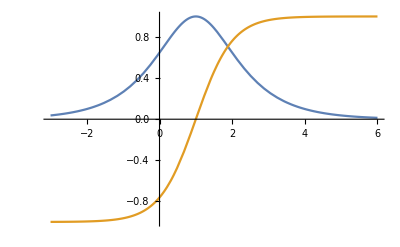

```mathematica
Plot[{Sech[t-1],Tanh[t-1]},{t,-3,6}]
```

```mathematica
D[Cos[k x]^2 +A Cos[k/2 x+π ϕ]^2- 2*B Sin[θ] Sin[2 k/2 x+π]/.{k->2π,ϕ->0},x]==0//FullSimplify
```

(A+4 Cos[2 π x]) Sin[2 π x]==4 B Cos[2 π x] Sin[θ]

```mathematica
({{1/(√2), -1/(√2), 0, 0}, {1/(√2), 1/(√2), 0, 0}, {0, 0, 1/(√2), 1/(√2)}, {0, 0, 1/(√2), -1/(√2)}}).({{-Δs, 0, -J, -J}, {0, Δs, -J, -J}, {-J, -J, U, 0}, {-J, -J, 0, U}}).({{1/(√2), 1/(√2), 0, 0}, {-1/(√2), 1/(√2), 0, 0}, {0, 0, 1/(√2), 1/(√2)}, {0, 0, 1/(√2), -1/(√2)}})//MatrixForm
```

(0 | -Δs | 0 | 0
-Δs | 0 | -√2 J | 0
0 | -√2 J | U | 0
0 | 0 | 0 | U)

```mathematica
Eigensystem[({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})]//MatrixForm
```

(0 | 1/2 (U-√(16 J^2+U^2)) | 1/2 (U+√(16 J^2+U^2))
{1,0,0} | {0,-(-U-√(16 J^2+U^2))/(4 J),1} | {0,-(-U+√(16 J^2+U^2))/(4 J),1})

```mathematica
FullSimplify[Series[Eigensystem[({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})],{J,0,2}],Assumptions->{U>0}]//MatrixForm//Normal
```

(0 | -(4 J^2)/U | (4 J^2)/U+U
{1,0,0} | {0,(2 J)/U+U/(2 J),1} | {0,-(2 J)/U,1})

```mathematica
Series[Evaluate[Normalize/@(Eigensystem[({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})][[2,All]])],{J,0,2}]
```

{{1,0,0},{0,((U+√(U^2))/J+(8 J)/(√(U^2))+O[J]^3)/(√(16+Abs[(-U-√(16 J^2+U^2))/J]^2)),1/(√(1+1/16 Abs[(-U-√(16 J^2+U^2))/J]^2))},{0,((U-√(U^2))/J-(8 J)/(√(U^2))+O[J]^3)/(√(16+Abs[(-U+√(16 J^2+U^2))/J]^2)),1/(√(1+1/16 Abs[(-U+√(16 J^2+U^2))/J]^2))}}

```mathematica
FullSimplify[Eigensystem[({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})]/.{J->(√3)/4 U},Assumptions->{U>0}][[All]]//MatrixForm
```

(0 | -U/2 | (3 U)/2
{1,0,0} | {0,√3,1} | {0,-1/(√3),1})

```mathematica
eigensys = FullSimplify[Eigensystem[({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})]/.{J->(√3)/4 U},Assumptions->{U>0}];
eigenva = eigensys[[1,All]]
eigenve =Normalize/@eigensys[[2,All]];
eigenve//MatrixForm
```

{0,-U/2,(3 U)/2}

(1 | 0 | 0
0 | (√3)/2 | 1/2
0 | -1/2 | (√3)/2)

```mathematica
MatrixExp[I ({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})t/(U/2)/.{J->(√3)/4 U}]//FullSimplify//MatrixForm
```

(1 | 0 | 0
0 | 1/4 ⅇ^(-ⅈ t) (3+ⅇ^(4 ⅈ t)) | √3 Cos[t] Sin[t] (-ⅈ Cos[t]+Sin[t])
0 | √3 Cos[t] Sin[t] (-ⅈ Cos[t]+Sin[t]) | 1/4 ⅇ^(-ⅈ t) (1+3 ⅇ^(4 ⅈ t)))

```mathematica
MatrixExp[-I ({{0, 0, 0}, {0, 0, -2J}, {0, -2J, U}})t/(U/2)/.{J->(√3)/4 U}].{1/(√2),1/(√2),0}/.{t->π/2}//MatrixForm
```

(1/(√2)
ⅈ/(√2)
0)

```mathematica
({{1/(√2), 1/(√2), 0}, {-1/(√2), 1/(√2), 0}, {0, 0, 1}}).Transpose[eigenve].MatrixExp[-I  t/(U/2)DiagonalMatrix[eigenva]].eigenve.({{1/(√2), -1/(√2), 0}, {1/(√2), 1/(√2), 0}, {0, 0, 1}}).{1,0,0}/.{t->π/2}//FullSimplify//MatrixForm
MatrixExp[-I  t/(U/2)DiagonalMatrix[eigenva]].eigenve.({{1/(√2), -1/(√2), 0}, {1/(√2), 1/(√2), 0}, {0, 0, 1}}).{1,0,0}//FullSimplify
```

(1/2+ⅈ/2
-1/2+ⅈ/2
0)

{1/(√2),1/2 √(3/2) ⅇ^(ⅈ t),-ⅇ^(-3 ⅈ t)/(2 √2)}

```mathematica
MatrixExp[-I  t/(U/2)DiagonalMatrix[eigenva]]/.{t->π/2}
```

{{1,0,0},{0,ⅈ,0},{0,0,ⅈ}}

```mathematica
({{1/(√2), -1/(√2), 0}, {1/(√2), 1/(√2), 0}, {0, 0, 1}}).{1,0,0}
```

{1/(√2),1/(√2),0}